Clear::wrsym: 符号 GlobalClusteringCoefficient 被保护.

Clear::wrsym: 符号 GlobalPreferences 被保护.

Clear::wrsym: 符号 GlobalSession 被保护.

General::stop: 在本次计算中，Clear::wrsym 的进一步输出将被抑制.

成功收敛点数： 444/445

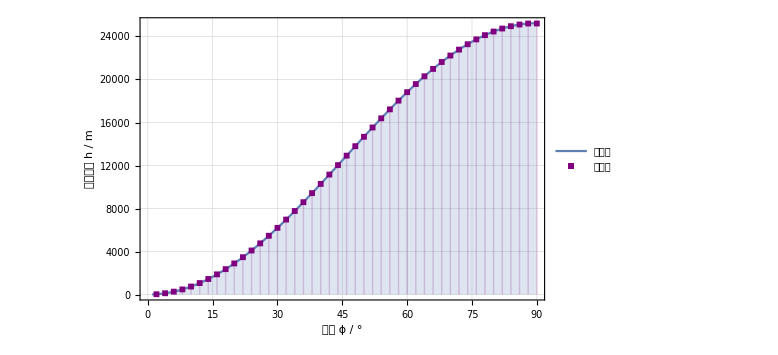

```mathematica
ClearAll[f,g];ClearAll;Clear["Global*"];

f[h_?NumericQ,ϕ_?NumericQ]:=Module[{R=6.3710087666*^6,ω=2 π/86400,μ=6.67430*^-11*5.9722*^24,a,b,c,e,p,α1},a=μ (R+h)/(2 μ-(R+h)^3 ω^2 Cos[ϕ]^2);
b=Sqrt[((R+h)^5 ω^2 Cos[ϕ]^2)/(2 μ-(R+h)^3 ω^2 Cos[ϕ]^2)];
c=Sqrt[a^2-b^2];
e=c/a;p=b^2/a;
α1=ArcCos[(R-p)/(e R)];
(ArcTan[Tan[α1]/Cos[ϕ]]-p^2/((R+h)^2 Cos[ϕ])/(1-e^2)*((e Sin[α1])/(1-e Cos[α1])+2/Sqrt[1-e^2]*ArcTan[Sqrt[(1+e)/(1-e)]*Tan[α1/2]]))*R*Cos[ϕ]];

g[h_?NumericQ,ϕ_?NumericQ]:=Module[{R=6.3710087666*^6,ω=2 π/86400,μ=6.67430*^-11*5.9722*^24,a,b,c,e,p,α1},a=μ (R+h)/(2 μ-(R+h)^3 ω^2 Cos[ϕ]^2);
b=Sqrt[((R+h)^5 ω^2 Cos[ϕ]^2)/(2 μ-(R+h)^3 ω^2 Cos[ϕ]^2)];
c=Sqrt[a^2-b^2];
e=c/a;p=b^2/a;
α1=ArcCos[(R-p)/(e R)];
(ArcTan[Sin[ϕ]/Sqrt[Tan[α1]^2+Cos[ϕ]^2]]-ϕ) R];
ClearAll[FG];
FG[h_?NumericQ,ϕ_?NumericQ]:=Module[{v},v=Quiet@Check[N[f[h,ϕ]+g[h,ϕ],$MachinePrecision],(* 用机器精度求值*)Indeterminate];
v=Chop[v,10^-12];(*把 10^-12 以下虚部切零*)If[NumericQ[v]&&Im[v]==0,Re[v],Indeterminate]];
seed={{2,30.5},{4,120.5},{6,270},{8,478.5},{10,745},{12,1068},{14,1446.5},{16,1878},{18,2361.5},{20,2894},{22,3474},{24,4097.5},{26,4762.5},{28,5465.5},{30,6203.5},{32,6973},{34,7770},{36,8591},{38,9432.5},{40,10290},{42,11159},{44,12036},{46,12917},{48,13796.5},{50,14671.5},{52,15537},{54,16388.5},{56,17222.5},{58,18034.5},{60,18820.5},{62,19576.5},{64,20298.5},{66,20983},{68,21626.5},{70,22226},{72,22778},{74,23279.5},{76,23728.5},{78,24123},{80,24459.5},{82,24738},{84,24955.5},{86,25112},{88,25206},{90,25206}};
hGuess[ϕ_?NumericQ]:=Interpolation[seed,Method->"Spline"][ϕ];

(* ——最小可行 hRoot：双点 Secant，不要求异号——*)ClearAll[hRoot];
hRoot[ϕdeg_?NumericQ]:=Module[{ϕ=N[ϕdeg Degree],h0=hGuess[ϕdeg],h1,root},If[!NumericQ[h0]||h0<=0,Return@Indeterminate];
(*用 5% 上偏值作第二初猜；可改 1%–10%*)h1=1.05 h0;
root=Quiet@Check[h/. FindRoot[FG[h,ϕ]==0,{h,h0,h1},(*Secant 两点初值*)Method->"Secant",(*不要求端点异号:contentReference[oaicite:1]{index=1}*)WorkingPrecision->30,(*足够高精又不会触发复数域错:contentReference[oaicite:2]{index=2}*)AccuracyGoal->8,MaxIterations->200],Indeterminate];
If[NumericQ[root]&&root>0,root,Indeterminate]]

(*h40=hRoot[40]          (* ≈10290. 如果得到正数就说明已经成功*)*)


ϕGrid=Range[1,89.8,0.2];
auto=Cases[Table[{ϕ,hRoot[ϕ]},{ϕ,ϕGrid}],{x_Real,y_Real}];

Print["成功收敛点数： ",Length[auto],"/",Length[ϕGrid]];
ListLinePlot[{auto,seed},Joined->{True,False},PlotStyle->{Thick,Purple},PlotMarkers->{None,{Automatic,6}},PlotLegends->{"数值根","粗算点"},AxesLabel->{"纬度 ϕ / °","所需高度 h / m"},ImageSize->Large,PlotTheme->"Detailed",Filling->Axis]
```

```mathematica
ϕ=40 Degree;
h0=hGuess[40]          (*预期≈1.029×10^4*)

FG[h0,ϕ]
```

10290.

0.000364453

成功收敛点数： 0/440

ListLinePlot::lpn: {{},{{2.,30.5},{4.,120.5},{6.,270.},{8.,478.5},{10.,745.},{12.,1068.},{14.,1446.5},{16.,1878.},{18.,2361.5},{20.,2894.},«35»}} 不是由数字或者数对组成的列表.

ListLinePlot[{{},{{2,30.5},{4,120.5},{6,270},{8,478.5},{10,745},{12,1068},{14,1446.5},{16,1878},{18,2361.5},{20,2894},{22,3474},{24,4097.5},{26,4762.5},{28,5465.5},{30,6203.5},{32,6973},{34,7770},{36,8591},{38,9432.5},{40,10290},{42,11159},{44,12036},{46,12917},{48,13796.5},{50,14671.5},{52,15537},{54,16388.5},{56,17222.5},{58,18034.5},{60,18820.5},{62,19576.5},{64,20298.5},{66,20983},{68,21626.5},{70,22226},{72,22778},{74,23279.5},{76,23728.5},{78,24123},{80,24459.5},{82,24738},{84,24955.5},{86,25112},{88,25206},{90,25206}}},Joined→{True,False},PlotStyle→{Thickness[Large],RGBColor[0.5, 0, 0.5]},PlotMarkers→{None,{Automatic,6}},PlotLegends→{单点初值求得的根,手算/文献点},AxesLabel→{纬度 ϕ / °,所需高度 h / m},ImageSize→Large]

```mathematica
ϕtest=40;
h0=hGuess[ϕtest]          (* ≈10290*)
FindRoot[f[h,ϕtest Degree]+g[h,ϕtest Degree]==0,{h,h0},WorkingPrecision->50,AccuracyGoal->12,MaxIterations->500]
```

10290.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 50. 位的工作精度以满足这些容差.

{h→10289.568157396556371177755880555957109507249265058}

```mathematica
N[f[h0,ϕtest Degree]+g[h0,ϕtest Degree],30]
```

0.000364453